# Covid-19 Infections and Spread at SMU

## began 8/29/2020; Last Updated 9/1/2020

Move-in day was August 17, classes began on August 24
Infections recorded for the days on which SMU was notified of a positive test
Active cases reported by SMU: https://blog.smu.edu/coronavirus-covid-19/cases/

Non-active cases reported by SMU: https://blog.smu.edu/coronavirus-covid-19/cases/non-active-cases/

## Plotting Raw Data:

## Plotting cumulative cases:

```mathematica
activetotCase={0,0,0,2,2,3,5,5,13,25,38,46,68,77,99,106};
```

```mathematica
inactivetotCase={1,2,8};
```

```mathematica
activeonCase={0,0,0,1,1,1,3,3,7,12,16,21,36,42,51,55};
```

```mathematica
inactiveonCase={1,1,5};
```

Total Cases:

```mathematica
totCase2={1,2,8,10,10,11,13,13,21,33,46,54,76,85,107,114};
```

On-Campus:

```mathematica
onCase2={1,1,5,6,6,6,8,8,12,17,21,26,41,47,56,60};
```

Off-Campus:

```mathematica
offCase2=totCase2-onCase2;
```

```mathematica
DayList2=Range[0,Length[totCase2]-1];
```

```mathematica
totCase3=Inner[List,DayList2,totCase2,List];
```

```mathematica
onCase3=Inner[List,DayList2,onCase2,List];
```

```mathematica
offCase3=Inner[List,DayList2,offCase2,List];
```

```mathematica
plotnew=Show[ListLinePlot[{totCase3,onCase3,offCase3},GridLines->{{{7,Gray}},None},PlotStyle->{Blue,Orange,Green},PlotLabel->"SMU Covid-19 Cases",AxesLabel->{"Days Since Move-In","Total Confirmed Infections"},ImageSize->Large,PlotLegends->Placed[{"Total Cases","On-Campus","Off-Campus (Students+Employees)"},Below]],ListPlot[{Callout[{7,totCase2[[Length[totCase2]]]/2},"Classes Start",Left]}]]
```

-Graphics-

```mathematica
plotdot2=ListPlot[{totCase2,onCase2,offCase2},GridLines->{{{7,Gray}},None},PlotStyle->{Blue,Orange,Green},PlotLabel->"SMU Covid-19 Cases",AxesLabel->{"Days Since Move-In","Total Confirmed Infections"},ImageSize->Large,PlotLegends->Placed[{"Total Cases","On-Campus","Off-Campus (Students+Employees)"},Below]];
```

```mathematica
plotdoton2=ListPlot[{onCase2},GridLines->{{{7,Gray}},None},PlotStyle->{Blue},PlotLabel->"SMU Covid-19 Cases",AxesLabel->{"Days Since Move-In","Total Confirmed Infections"},ImageSize->Large,PlotLegends->Placed[{"On-Campus"},Below]];
```

```mathematica
gft2=N[(totCase2[[Length[totCase2]]]-totCase2[[Length[totCase2]-1]])/(totCase2[[Length[totCase2]-1]]-totCase2[[Length[totCase2]-2]])]
```

0.318182

```mathematica
gf[t_]:=(totCase2[[t]]-totCase2[[t-1]])/(totCase2[[t-1]]-totCase2[[t-2]]);
```

Power::infy: Infinite expression 1/0 encountered.

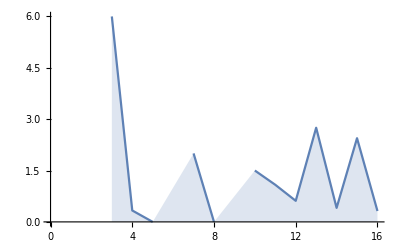

```mathematica
gfplottot=DiscretePlot[gf[t],{t,0,Length[totCase2]},Joined->True]
```

### New Cases Per day:

```mathematica
newtot=Table[(totCase2[[x+1]]-totCase2[[x]]),{x,1,Length[totCase2]-1}];
```

```mathematica
newon=Table[(onCase2[[x+1]]-onCase2[[x]]),{x,1,Length[onCase2]-1}];
```

```mathematica
newoff=newtot-newon;
```

```mathematica
DayList3=Range[1,Length[totCase2]-1];
```

```mathematica
newtot1=Inner[List,DayList3,newtot,List];
```

```mathematica
newon1=Inner[List,DayList3,newon,List];
```

```mathematica
newoff1=Inner[List,DayList3,newoff,List];
```

```mathematica
plotnew=Show[ListPlot[{newtot1,newon1,newoff1},GridLines->{{{7,Gray}},None},PlotStyle->{Blue,Orange,Green},PlotLabel->"SMU Covid-19 Cases",AxesLabel->{"Days Since Move-In","New Confirmed Infections"},ImageSize->Large,PlotLegends->Placed[{"Total Cases","On-Campus","Off-Campus (Students+Employees)"},Below],Filling->Axis],ListPlot[{Callout[{7,newtot[[Length[newtot]]]},"Classes Start",Left]}]]
```

-Graphics-

## Models for Total Infections:

## Models for On-Campus Spread:

### On-Campus Model 2 (exponential):

```mathematica
nlm4=NonlinearModelFit[onCase2,K Exp[β x],{K,β},x];
```

```mathematica
v4[x_]:=Normal[nlm4];
```

```mathematica
plot4=Show[Plot[v4[x],{x,0,Length[totCase2]},PlotRange->All,PlotStyle->{Red,Thick},GridLines->{{{7,Gray}},None},AxesLabel->{"Days Since Move-In","Total Confirmed Infections"},ImageSize->Large,PlotLabel->"SMU Covid-19 On-Campus Cases Model 2"],ListPlot[{Callout[{7,totCase2[[Length[totCase2]]]/2},"Classes Start",Left]}]];
```

```mathematica
Show[plot4,plotdot2]
```

-Graphics-

```mathematica
Show[plot4,plotdoton2]
```

-Graphics-

```mathematica
resids4=nlm4["FitResiduals"];
```

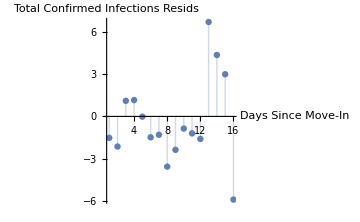

```mathematica
ListPlot[resids4,Filling->Axis,PlotRange->All,AxesLabel->{"Days Since Move-In","Total Confirmed Infections Resids"},ImageSize->Medium]
```

```mathematica
Grid[Transpose[{#,nlm4[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
```

AdjustedRSquared | 0.98679
AIC | 86.6736
BIC | 88.9913
RSquared | 0.988441

## When do we go home?

Assuming that this simple exponential model is fairly accurate and that the current behavior of the spreading continues.

#### Model 2:

```mathematica
NSolve[maxon==nlm4[Length[onCase2]-1+days],days]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{days→13.5006}}